## Attempt to Solve a simpler boundary with eigenmodes method

Try this eigenmodes approach for a shape where an analytic solution is available  (using perturbation theory)

```mathematica
r0[A_,θ_] = 1 + A Cos[4θ];
```

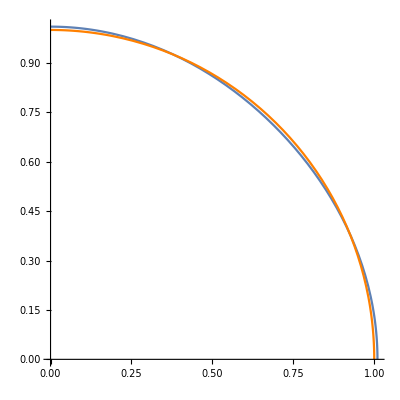

```mathematica
Show[ParametricPlot[{r0[0.01,θ]Cos[θ],r0[0.01,θ]Sin[θ]},{θ,0,π/2}],ParametricPlot[{Cos[θ],Sin[θ]},{θ,0,π/2},PlotStyle->Orange]]
```

Construct a list of coefficients for matrix  . Take advantage of 4-fold symmetry &  θ ↔ -θ symmetry. Only Cos(4mθ) Fourier modes are nonvanishing

```mathematica
I0term[A_] := 4NIntegrate[Log[r0[A,θ]],{θ,0,π/2}]
```

```mathematica
Ikterm[A_,k_] :=4 NIntegrate[Log[r0[A,θ]] Cos[4k θ],{θ,0,π/2}]
```

```mathematica
Ckterm[A_,k_,m_] := 4 NIntegrate[(r0[A,θ])^(4m) Cos[4m θ]Cos[4k θ],{θ,0,π/2}]
```

```mathematica
CoeffList[A_,M0_] := Chop[Table[Ckterm[A,k,m],{m,1,M0},{k,0,M0}]]
```

Now build the matrix  (see notes). Choose A small, such that comparison with analytic solution is possible (if so desired). I would expect that with 20 modes one should get pretty good convergence.

```mathematica
MM = Transpose[Join[{Join[{2π},Table[0,{j,1,20}]]},CoeffList[0.01,20]]];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {0.107354}. NIntegrate obtained -9.54098×10^-17 and 1.15407×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.81725×10^-8}. NIntegrate obtained -1.31839×10^-16 and 3.05222×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.81725×10^-8}. NIntegrate obtained -1.75207×10^-16 and 3.35444×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::levmaxord: (1+0.01 Cos[4 θ])^40 is a Levin function of differential order 12157665459056928800 which exceeds value of option "MaxOrder" -> 50. Treating (1+0.01 Cos[4 θ])^40 as a non-Levin function.

General::stop: Further output of NIntegrate::levmaxord will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Print[MM]
```

{{2 π,0.125673,0.00439933,0.000172865,7.15184×10^-6,3.04687×10^-7,1.32284×10^-8,5.81978×10^-10,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,3.14301,0.125752,0.00518849,0.000220169,9.52646×10^-6,4.17962×10^-7,1.85275×10^-8,8.27827×10^-10,0,0,0,0,0,0,0,0,0,0,0,0},{0,0.0628381,3.14599,0.188755,0.00943908,0.000448438,0.0000209038,9.66897×10^-7,4.4586×10^-8,2.05403×10^-9,0,0,0,0,0,0,0,0,0,0,0},{0,0.000471249,0.12573,3.15197,0.251988,0.0149606,0.000796911,0.0000403136,1.98279×10^-6,9.59094×10^-8,4.59094×10^-9,2.18259×10^-10,0,0,0,0,0,0,0,0,0},{0,1.5708×10^-6,0.00219966,0.188755,3.16046,0.315504,0.0217605,0.00129131,0.0000708746,3.71547×10^-6,1.89172×10^-7,9.4445×10^-9,4.65086×10^-10,0,0,0,0,0,0,0,0},{0,1.9635×10^-9,0.0000219939,0.00518752,0.251988,3.17149,0.37938,0.0298491,0.00195769,0.000116234,6.49207×10^-6,3.48254×10^-7,1.81641×10^-8,9.28365×10^-10,0,0,0,0,0,0,0},{0,0,1.37453×10^-7,0.0000864327,0.00943908,0.315504,3.18507,0.443692,0.0392388,0.00282242,0.000180577,0.0000107279,6.0609×10^-7,3.30393×10^-8,1.75415×10^-9,0,0,0,0,0,0},{0,0,5.49791×10^-10,9.72202×10^-7,0.000220126,0.0149606,0.37938,3.20121,0.508518,0.0499442,0.00391226,0.000268632,0.0000169374,1.00676×10^-6,5.73407×10^-8,3.1631×10^-9,1.70242×10^-10,0,0,0,0},{0,0,0,7.7768×10^-9,3.57592×10^-6,0.000448438,0.0217605,0.443692,3.21993,0.573935,0.0619817,0.00525441,0.000385684,0.0000257459,1.60779×10^-6,9.56087×10^-8,5.47835×10^-9,3.04973×10^-10,0,0,0},{0,0,0,0,4.29024×10^-8,9.52456×10^-6,0.000796911,0.0298491,0.508518,3.24125,0.640023,0.0753701,0.00687656,0.000537589,0.0000379011,2.48273×10^-6,1.53997×10^-7,9.16093×10^-9,5.2737×10^-10,0,0},{0,0,0,0,3.93218×10^-10,1.52343×10^-7,0.0000209038,0.00129131,0.0392388,0.573935,3.2652,0.70686,0.0901302,0.00880692,0.000730784,0.0000542851,3.72396×10^-6,2.40672×10^-7,1.48535×10^-8,8.83871×10^-10,0},{0,0,0,0,0,1.90386×10^-9,4.17877×10^-7,0.0000403136,0.00195769,0.0499442,0.640023,3.2918,0.774527,0.106285,0.0110743,0.000972302,0.0000759269,5.44575×10^-6,3.66281×10^-7,2.34341×10^-8,1.4407×10^-9},{0,0,0,0,0,0,6.61419×10^-9,9.66897×10^-7,0.0000708746,0.00282242,0.0619817,0.70686,3.32108,0.843106,0.12386,0.0137083,0.00126979,0.000104015,7.78761×10^-6,5.44488×10^-7,3.60813×10^-8},{0,0,0,0,0,0,0,1.85237×10^-8,1.98279×10^-6,0.000116234,0.00391226,0.0753701,0.774527,3.35309,0.91268,0.142882,0.0167389,0.00163153,0.000139911,0.0000109179,7.92579×10^-7},{0,0,0,0,0,0,0,2.90986×10^-10,4.45859×10^-8,3.71547×10^-6,0.000180577,0.00525441,0.0901302,0.843106,3.38785,0.983332,0.163382,0.0201972,0.00206645,0.000185164,0.0000150376},{0,0,0,0,0,0,0,0,8.27654×10^-10,9.59094×10^-8,6.49207×10^-6,0.000268632,0.00687656,0.106285,0.91268,3.42542,1.05515,0.185391,0.024115,0.00258416,0.000241522},{0,0,0,0,0,0,0,0,0,2.05403×10^-9,1.89172×10^-7,0.0000107279,0.000385684,0.00880692,0.12386,0.983332,3.46582,1.12821,0.208944,0.028525,0.00319493},{0,0,0,0,0,0,0,0,0,0,4.59094×10^-9,3.48254×10^-7,0.0000169374,0.000537589,0.0110743,0.142882,1.05515,3.50912,1.20262,0.234077,0.0334607},{0,0,0,0,0,0,0,0,0,0,0,9.4445×10^-9,6.0609×10^-7,0.0000257459,0.000730784,0.0137083,0.163382,1.12821,3.55536,1.27846,0.260831},{0,0,0,0,0,0,0,0,0,0,0,2.18257×10^-10,1.81641×10^-8,1.00676×10^-6,0.0000379011,0.000972302,0.0167389,0.185391,1.20262,3.6046,1.35582},{0,0,0,0,0,0,0,0,0,0,0,0,4.65086×10^-10,3.30394×10^-8,1.60779×10^-6,0.0000542851,0.00126979,0.0201972,0.208944,1.27846,3.65689}}

Now construct the inhomogeneous term (vector of length M0+1)

```mathematica
II = Join[{I0term[0.01]},Chop[Table[Ikterm[0.01,m],{m,1,20}]]];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.81725×10^-8}. NIntegrate obtained -4.09248×10^-15 and 4.21196×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.81725×10^-8}. NIntegrate obtained 7.75205×10^-18 and 2.91877×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.46646}. NIntegrate obtained -1.26445×10^-17 and 9.26113×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
Print[II]
```

{-0.000157086,0.0314167,-0.0000785437,2.61819×10^-7,-9.81846×10^-10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

The Fourier coefficients Am are obtained by solving the system of linear equations

```mathematica
AM3 = Inverse[MM]. II;
```

```mathematica
Print[AM3]
```

{-0.000224953,0.0100048,-0.000225256,7.59678×10^-6,-3.0354×10^-7,1.33215×10^-8,-6.20648×10^-10,3.01392×10^-11,-1.50891×10^-12,7.74397×10^-14,-4.05621×10^-15,2.15753×10^-16,-1.15182×10^-17,5.92296×10^-19,-2.73414×10^-20,1.00069×10^-21,-2.28306×10^-23,1.33891×10^-24,-5.57207×10^-25,1.27259×10^-25,-1.88407×10^-26}

Now construct the potential ϕ. Express it in Cartesian coordinates, so that it is possible to make a contour plot.

```mathematica
ϕ20[x_,y_] = Log[r] + AM3[[1]] + Table[Cos[4k θ]r^(4k),{k,1,20}].Take[AM3,-20] /. {r-> √(x^2+y^2),θ ->  ArcTan[y/x]} ;
```

```mathematica
Print[ϕ20[1,1]]
```

0.302145

Make the contour plot ϕ=0, and compare it with the curve r0(θ).

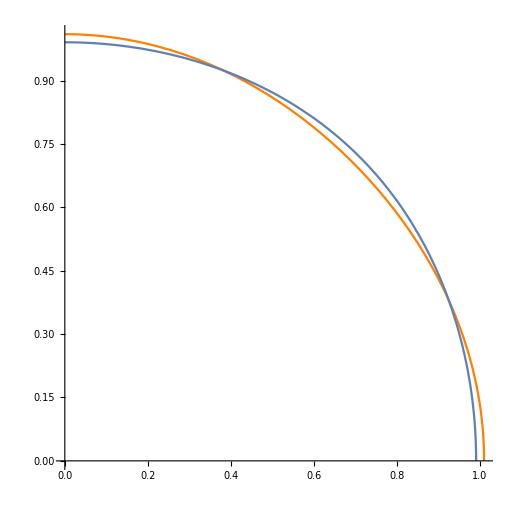

```mathematica
Show[ParametricPlot[{r0[0.01,θ]Cos[θ],r0[0.01,θ]Sin[θ]},{θ,0,π/2},PlotStyle->Orange],ContourPlot[ϕ20[x,y]==0,{x,0,1},{y,0,1}]]
```

Agreement doesn’t seem to be good. Increasing number of modes doesn’t seem to help much.

## Analytic solution (perturbation theory assuming A ≪ 1 )

## (see note attached - where the Fourier coefficients are expressed through expansion in A )

Define the analytic solution (O(A)) .

```mathematica
ϕAna[x_,y_,M_,ϵ_] := Log[r] + 2 ϵ^2 - ϵ Cos[4θ] + Total[Table[(-1)^m ϵ^m 2^(m-1)Factorial[m-1] r^m Cos[4m θ],{m,2,M}]] /. {r-> √(x^2+y^2),θ ->  ArcTan[y/x]} ;
```

Let’s try first with amplitude 0.1 . (Note that Manipulate make take a couple second to settle when you switch values of M. In my machine it’s better to change M manually (by pressing “+“ and let it settle) rather than let it run in a continuum mode).

```mathematica
With[{ϵ=0.1},Manipulate[Show[ParametricPlot[{r0[ϵ,θ]Cos[θ],r0[ϵ,θ]Sin[θ]},{θ,0,π/2},PlotStyle->Orange],ContourPlot[ϕAna[x,y,M,ϵ]==0,{x,0,1.3},{y,0,1.3}]],{M,0,20,1}]]
```

What one can see is that the best approximation is obtained with a small number of modes (around 3 - 4). Using a larger number of modes the approximation gets worse, rather than better. This seems to me as indicative that the underlying the approximation there is asymptotic (Poincare) expansion, rather than a converging  (Taylor) expansion.  If you are not familiar with these concepts (most physics students are not ..), look here : https : // en.wikipedia.org/wiki/Asymptotic_expansion (the book of Bender and Orszag in the reference list is a good basic source or here: https://ncatlab.org/nlab/show/asymptotic+expansion

Try now with smaller amplitude.

```mathematica
With[{ϵ=0.05},Manipulate[Show[ParametricPlot[{r0[ϵ,θ]Cos[θ],r0[ϵ,θ]Sin[θ]},{θ,0,π/2},PlotStyle->Orange],ContourPlot[ϕAna[x,y,M,ϵ]==0,{x,0,1.3},{y,0,1.3}]],{M,0,40,1}]]
```

One can see in the above that for a smaller amplitude, the “optimal truncation” (also called “superasymptotics”) phenomenon occurs at a larger number of Fourier modes. Again, this is consistent with the behavior of asymptotic expansions.  Denoting by N_opt(ϵ) the “optimal” number of Fourier modes for a given amplitude ϵ, we may thus expect that N_opt(ϵ) ⟶ ∞ only for ϵ⟶0.